# Aliquot Sequence

"THE CHALLENGE"

In an aliquot sequence, each term is the sum of the proper divisors of the previous term.

Write a function that finds the aliquot sequence starting with a given positive integer. Stop at 1 or before a term is repeated.

## More Details

The proper divisors of a number do not include the number itself. For example, the proper divisors of 6 are 1, 2, 3, and 6 is called an improper divisor.

The aliquot sequence starting with a positive integer k can be defined in terms of the divisor function σ_1(x):

s_0 = k
s_n = σ_1(s_(n-1)) - s_(n-1),

where σ_1(x) gives the sum of all the divisors including x. The term s_(n-1) is therefore subtracted since it is the improper divisor. In the Wolfram Language σ_1 is implemented through "DivisorSigma"paclet:ref/DivisorSigmapaclet:ref/DivisorSigmaLinkHyperlinkActive.

For example, the proper divisors of 20 are 1, 2, 4, 5, 10, which add up to 22. The proper divisors of 22 are 1, 2, 11, which add up to 14, and so on. There are no proper divisors of 1.

It is not known whether all aliquot sequences eventually terminate or become periodic. For example, the fate of the aliquot sequence for 276 is unknown. Therefore, we only want to find the sequence for numbers like 276 up to a certain number of terms, say 100.

## What Your Function Should Do

Write a function called AliquotSequence that finds an aliquot sequence for a given positive integer. Stop at 1 or before a term is repeated. Restrict your function so that it will not produce more than 100 terms in the aliquot sequence for the given number.

```mathematica
AliquotSequence[20]
```

{20,22,14,10,8,7,1}

### More Examples

The proper divisors of 6 are 1, 2, 3, which add up to 6. If a number equals the sum of its proper divisors, it is called a perfect number.

```mathematica
AliquotSequence[6]
```

{6}

The sum of the proper divisors of 220 and the sum of the proper divisors of 284 are both 220. If two numbers are each the sum of the proper divisors of the other, they are called an amicable pair.

```mathematica
AliquotSequence[220]
```

{220,284}

```mathematica
AliquotSequence[25]
```

{25,6}

```mathematica
AliquotSequence[276]
```

{276,396,696,1104,1872,3770,3790,3050,2716,2772,5964,10164,19628,19684,22876,26404,30044,33796,38780,54628,54684,111300,263676,465668,465724,465780,1026060,2325540,5335260,11738916,23117724,45956820,121129260,266485716,558454764,1092873236,1470806764,1471882804,1642613196,2737688884,2740114636,2791337780,4946860492,4946860548,9344070652,9344070708,15573451404,27078171764,27284104204,27410152084,27410152140,76787720100,220578719452,254903331620,361672366300,603062136740,921203207260,1381419996068,1395444575644,1395478688996,1395546402460,2069258468900,3065057872156,3277068463844,3429776547484,3597527970596,4028517592540,5641400009252,5641400009308,5641400009364,9709348326636,16331909651988,31948891146732,54770416120644,100509779504316,208751080955844,388416032284476,749365894850244,1414070378301756,2556878765995204,2556878765995260,6726041614128900,15626498692840700,23762659088671300,35168735451235260,78257359358590020,186897487211247036,340813223900632644,592585414385033916,1326583294186844484,2594892903616159356,4946738730471899844,8244565422068579772,13740942370114299844,13780400058385352252,13780400058385352308,14272557426581383244,14272557426581383300,21155073391000330684,21374326697892540932}

"SCRATCH AREA"

```mathematica
AliquotSequence[n_Integer?Positive]:=Block[{go},
go[m_Integer?Positive,seq_List]:=
With[{div=DivisorSigma[1,m]-m},
If[m==1||Count[seq,div]>0||Length[seq]>99,
seq,
go[div,Append[seq,div]]
]];
go[n,{n}]
]
```

```mathematica
AliquotSequenceLength[n_Integer?Positive]:=Length[AliquotSequence[n]]
sequenceLengths=Table[AliquotSequenceLength[n],{n,1,1000}];
```

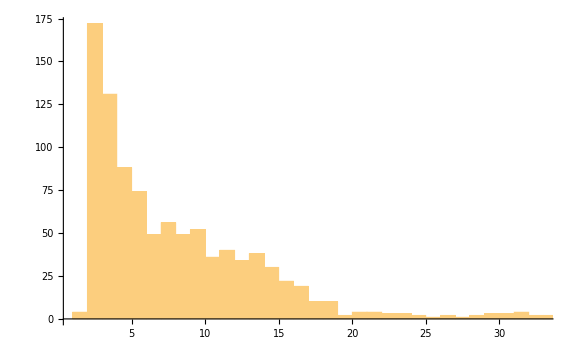

```mathematica
Histogram[sequenceLengths]
```

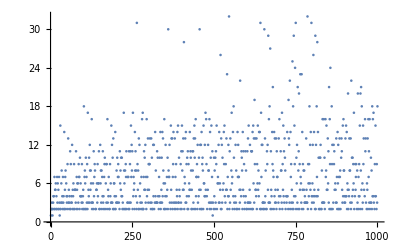

```mathematica
ListPlot[sequenceLengths]
```

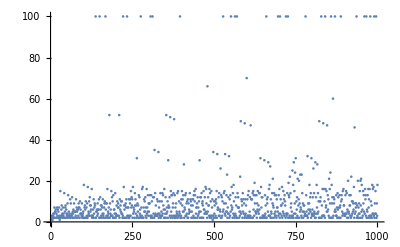

```mathematica
ListPlot[sequenceLengths,PlotRange->All]
```

```mathematica
CountLongAliquotSequences[n_Integer?Positive]:=Count[Table[AliquotSequenceLength[m],{m,1,n}],100]
```

```mathematica
countList = Table[CountLongAliquotSequences[n], {n, 1, 1000}];
```

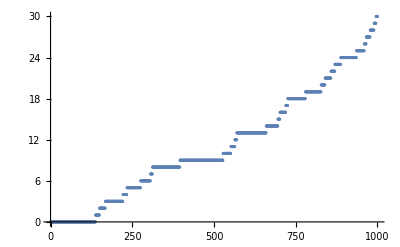

```mathematica
ListPlot[countList]
```

"ENTER YOUR CODE HERE"

```mathematica
AliquotSequence[n_Integer?Positive]:=Block[{go},
go[m_Integer?Positive,seq_List]:=
With[{div=DivisorSigma[1,m]-m},
If[m==1||Count[seq,div]>0||Length[seq]>99,
seq,
go[div,Append[seq,div]]
]];
go[n,{n}]
]
```